#### Problem 1

{ⅇ^(0.1 y) Cos[y],0.1 ⅇ^(0.1 y) x Cos[y]-ⅇ^(0.1 y) x Sin[y]}

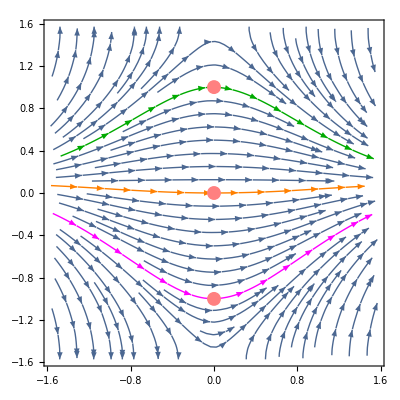

```mathematica
With[{func=x Exp[0.1y]Cos[y]},
Print[Grad[func,{x,y}]];StreamPlot[Evaluate@Grad[func,{x,y}],{x,-Pi/2,Pi/2},{y,-Pi/2,Pi/2},
StreamColorFunction->None,
StreamPoints->{{{{0,-1},Magenta},{{0,0},Orange},{{0,1},Darker[Green]},Automatic}},
Epilog->{ 
Pink,PointSize[0.025],Point/@{{0,-1},{0,0},{0,1}}
}
]
]
```

#### Problem 2

```mathematica
Probability[Z>0,Z\[Distributed]TransformedDistribution[X-Y,{X\[Distributed]NormalDistribution[10,1],Y\[Distributed]NormalDistribution[11,2]}
]
]
%//N
```

1/2 (1-Erf[1/(√10)])

0.32736

```mathematica
Solve[Evaluate[a+b(#1+1)+c(#1+1)#1==#2&@@@{{-1,1},{0,0},{1,1}}],{a,b,c}]
```

{{a→1,b→-1,c→1}}

```mathematica
Evaluate[a+b(#1+1)+c(#1+1)#1==#2&@@@{{-1,1},{0,0},{1,1}}]
```

{a==1,a+b==0,a+2 b+2 c==1}

```mathematica
A={{1,1,1},{0,1,3}}
```

{{1,1,1},{0,1,3}}

```mathematica
Transpose@A//MatrixForm
```

(1 | 0
1 | 1
1 | 3)

```mathematica
A.Transpose@A
```

{{3,4},{4,10}}

```mathematica
b={1,2,3}
```

{1,2,3}

```mathematica
A.b
```

{6,11}

```mathematica
(Transpose@A).{{1},{2},{3}}
```

Dot::dotsh: 张量 {{1,0},{1,1},{1,3}} 和 {{1},{2},{3}} 含有不兼容形状.

{{1,0},{1,1},{1,3}}.{{1},{2},{3}}

```mathematica
LinearSolve[A.Transpose@A,A.b]
```

{8/7,9/14}